```mathematica
(* If degree (highest power) is even then the nature of the polynomial function in the left and right side of the x will be similar (either both will go up or down) when x is very large.  If degree (highest power) is odd then the nature of the polynomial function in the left and right side of the x will be opposite (if one goes up the other will go down) when x is very large. If degree is even then then both side will go up when the coefficient of the term with highest power is positive and both will go down when it is negative. If degree is odd then the right side will go up and left side will go down when the coefficient of the term with highest power is positive and the reverse occurs when the coefficient is negative*)
```

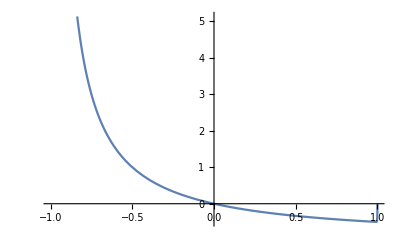

-Graphics-

```mathematica
f[x_]:=∑_(n=1)^1000 (-1)^n x^n;                          (* degree=1000 (even), coefficient of x^1000 is positive *)
Plot[f[x],{x, -1, 1}]
Plot[f[x],{x, -1.5, 1.5}]
```

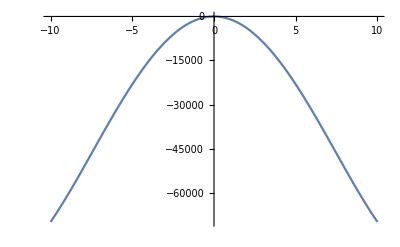

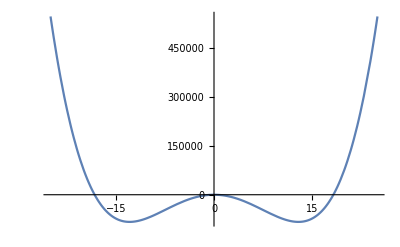

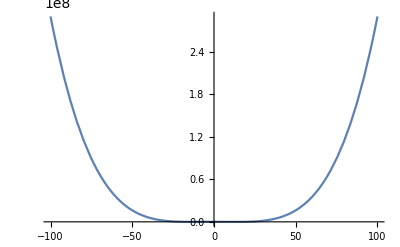

```mathematica
f[x_]:=3 x^4-1000 x^2;                       (* degree=4 (even), coefficient of x^4 is positive *)
Plot[f[x],{x, -10, 10}]
Plot[f[x],{x, -25, 25}]
Plot[f[x],{x, -100, 100}]
```

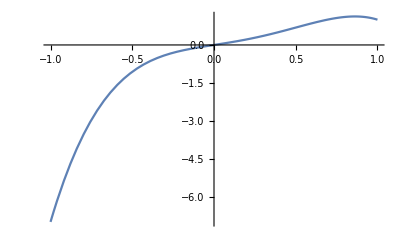

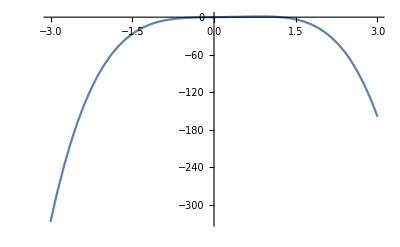

```mathematica
f[x_]:=-3 x^4+3 x^3+x;                 (* degree=4 (even), coefficient of x^4 is negative *)
Plot[f[x],{x, -1, 1}]
Plot[f[x],{x, -3, 3}]
```

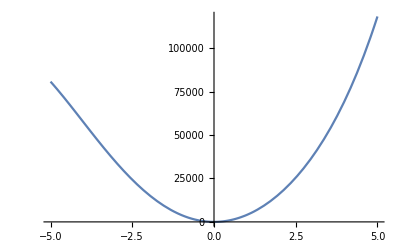

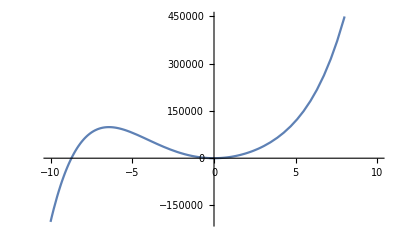

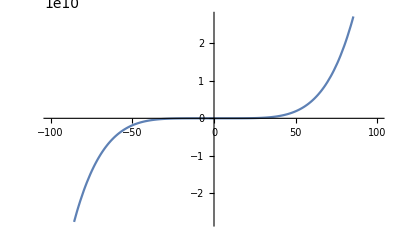

-Graphics-

```mathematica
f[x_]:=6 x^5+3980 x^2+x+5;          (* degree=5 (odd), coefficient of x^5 is positive *)
Plot[f[x],{x, -5, 5}]
Plot[f[x],{x, -10, 10}]
Plot[f[x],{x, -100, 100}]
Plot[f[x],{x, -1000, 1000}]
```

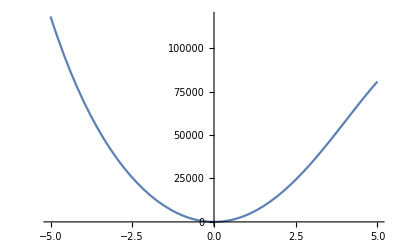

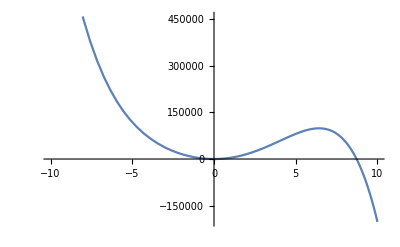

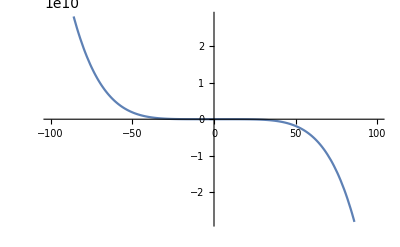

-Graphics-

```mathematica
f[x_]:=-6 x^5+3980 x^2+x+5;          (* degree=5 (odd), coefficient of x^5 is negative *)
Plot[f[x],{x, -5, 5}]
Plot[f[x],{x, -10, 10}]
Plot[f[x],{x, -100, 100}]
Plot[f[x],{x, -1000, 1000}]
```

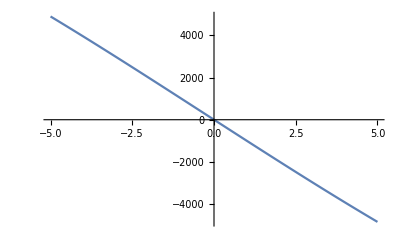

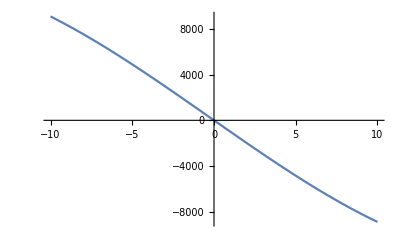

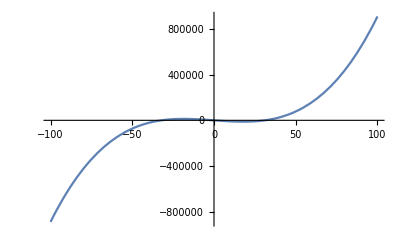

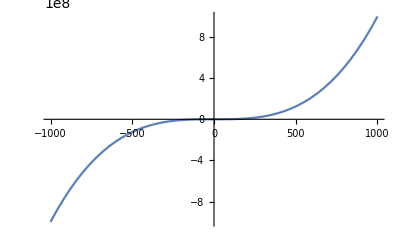

```mathematica
f[x_]:=x^3+x^2-1000x+1;            (* degree=3 (odd), coefficient of x^3 is positive *)
Plot[f[x],{x, -5, 5}]
Plot[f[x],{x, -10, 10}]
Plot[f[x],{x, -100, 100}]
Plot[f[x],{x, -1000, 1000}]
```

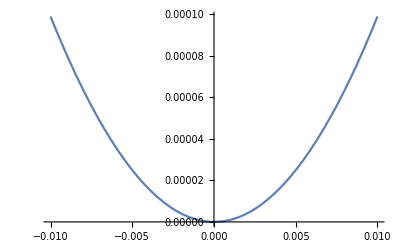

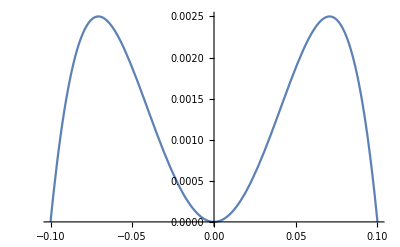

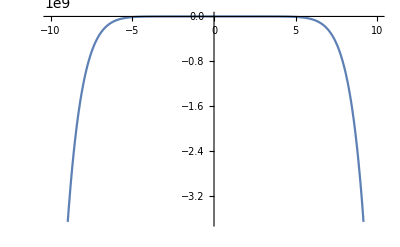

-Graphics-

-Graphics-

```mathematica
f[x_]:=-x^10+x^2-100 x^4+x^9;             (* degree=10 (even), coefficient of x^10 is negative *)
Plot[f[x],{x, -0.01, 0.01}]
Plot[f[x],{x, -0.1, 0.1}]
Plot[f[x],{x, -10, 10}]
Plot[f[x],{x, -100, 100}]
Plot[f[x],{x, -1000, 1000}]
```

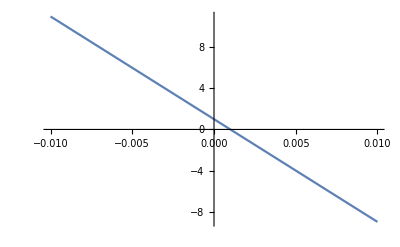

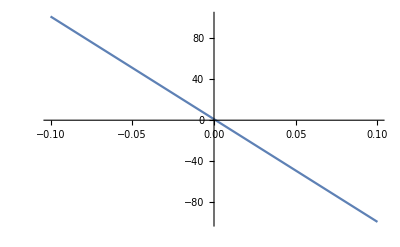

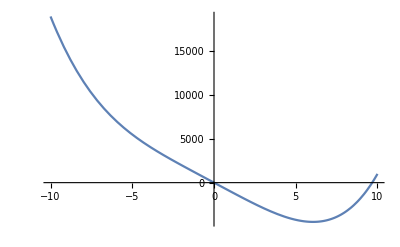

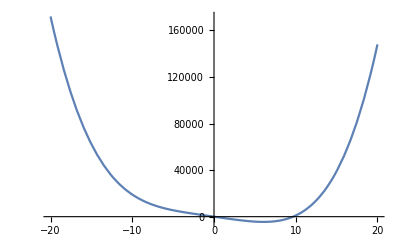

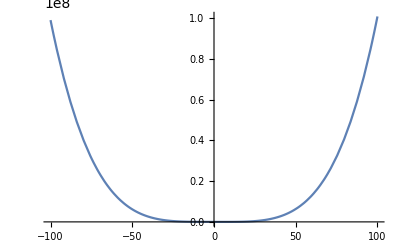

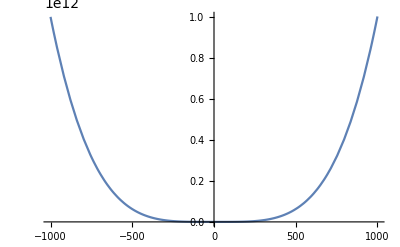

```mathematica
f[x_]:=x^3+x^4-1000x+1;                     (* degree=4 (even), coefficient of x^4 is positive *)
Plot[f[x],{x, -0.01, 0.01}]
Plot[f[x],{x, -0.1, 0.1}]
Plot[f[x],{x, -10, 10}]
Plot[f[x],{x, -20, 20}]
Plot[f[x],{x, -100, 100}]
Plot[f[x],{x, -1000, 1000}]
```